High order Ne.b4de.b4lec elements with local complete sequence properties
	Joachim Scho.a8berl and Sabine Zaglmayr

```mathematica
Needs["VectorAnalysis`"]
SetCoordinates[Cartesian[x,y,z]];
```

the Legendrepolynomials       l_i(x)  (i=0,...p)
	l_i(x):=ix

```mathematica
Clear[l]
```

```mathematica
l(i_,x_):=ix;
```

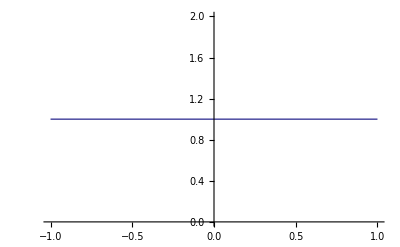
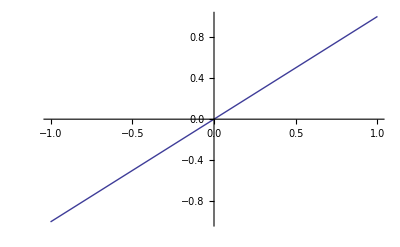
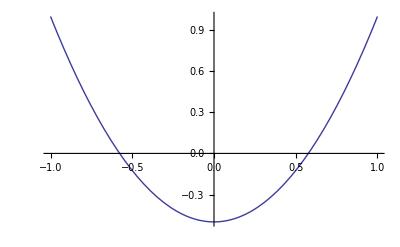
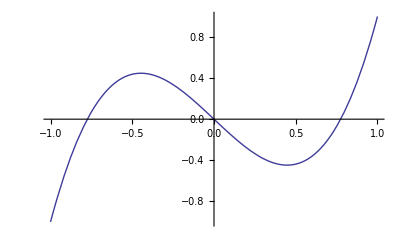
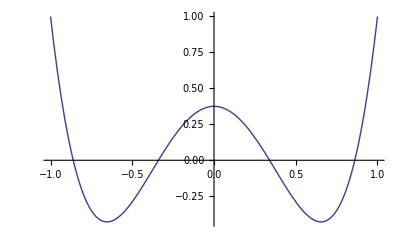
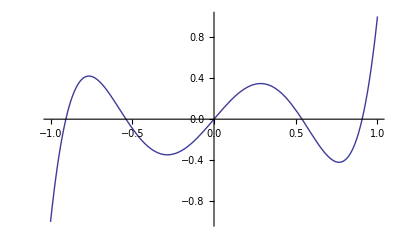

```mathematica
Table[Plot[l[i, x], {x,-1,1}], {i,0,5}]
```

theintegratedLegendre-polynomialsL_i(i=2,...,p)
L_i_[x_]:=∫_-1^x i-1zⅆz

```mathematica
L(i_,x_):=∫_-1^x l(i-1,z)ⅆz
```

```mathematica
For[i=2,i≤6,i++,    L(i,x_)=∫_-1^x l(i-1,z)ⅆz     ]
```

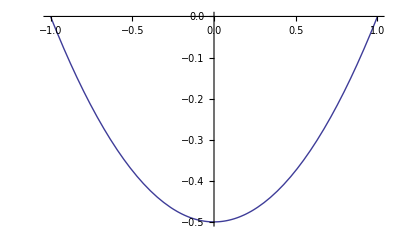
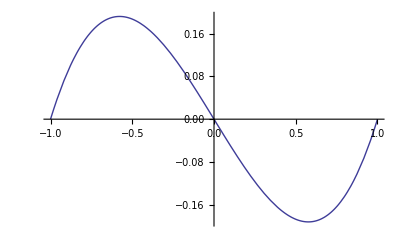
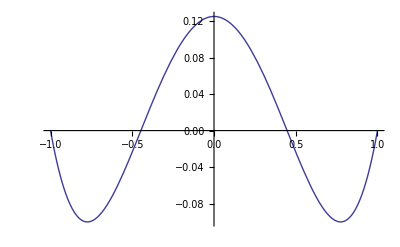
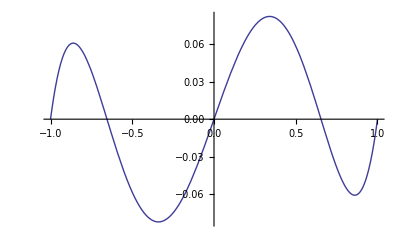

```mathematica
Table[Plot[L(i,x),{x,-1,1}],{i,2,5}]
```

the scaled Legendre polynomials

```mathematica
lS(n_,s_,t_):=Simplify[t^n l(n,s/t)];
```

```mathematica
Table[Plot3D[lS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the scaled integrated Legendre polynomials

```mathematica
LS(n_,s_,t_):=Simplify[t^n L(n,s/t)];
```

```mathematica
Table[Plot3D[LS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,2,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the barycentric coordinates
	λ_i (i=1,2,3,4)

```mathematica
Clear[point, lamda,px, edge,face]
point[0]={0,0,0};  point[1]={1,0,0}; point[2]={0,1,0}; point[3]={0,0,1};
edge[0]={0,1}; edge[1]={0,2};edge[2]={0,3}; edge[3]={1,2}; edge[4]={1,3}; edge[5]={2,3};
face[0]={0,1,2}; face[1]={0,1,3};face[2]={0,2,3};face[3]={1,2,3};

px={0,0,0};
For[i=0,i<4, ++i, px+=point[i]*lamda[i];]
sum=0;
For[i=0,i<4, ++i, sum+=lamda[i]];
px=Append[px, sum];
sol=Solve[px=={x,y,z,1}, {lamda[0],lamda[1], lamda[2], lamda[3]}];
lamda[0]=lamda[0]/.sol[[1]];
lamda[1]=lamda[1]/.sol[[1]];
lamda[2]=lamda[2]/.sol[[1]];
lamda[3]=lamda[3]/.sol[[1]];
```

```mathematica
Clear[lines];
lines={Thick};
For[i=0, i<6, i++,
p1= edge[i][[1]];
p2=edge[i][[2]];
line=Line[ { point[p1] ,point[ p2]  }  ] ;
lines=Append[lines, line];
]
Graphics3D[lines,Axes->True,AxesLabel->{x,y,z}, Boxed->True,ViewVertical->{0,0,1}]
```

-Graphics3D-

```mathematica
G[func_,fac0_]:=Module[{ncf, fac=fac0, cf},
ncf=16;
cf=Table[(-1+2/ncf*(i-1/2))*fac, {i,1,ncf} ];
 ContourPlot3D[func,{x,0,1},{y,0,1},{z,0,1},Contours->cf, RegionFunction->Function[{x,y,z}, lamda[0]>0], ColorFunction->ColorData["TemperatureMap"],
Mesh->None,ContourStyle->Directive[Opacity[0.5]]
 ] 
]
```

Hierarchical triangular H1- element  of order p using Scaled Legendre Polynomials

Vertex - based functions

```mathematica
phiV[i_]:=lamda[i];
```

Edge - based functions

```mathematica
phiE[m_,i_]:=LS[i, 
lamda[edge[m][[1]]]- lamda[edge[m][[2]]],
lamda[edge[m][[2]]]+ lamda[edge[m][[1]]] ];
```

Face-based functions

```mathematica
u[f_, i_]:=LS[i, lamda[face[f][[1]]]- lamda[face[f][[2]]],lamda[face[f][[1]]]+ lamda[face[f][[2]]] ];
v[f_,j_]:= lamda[face[f][[3]]]*lS[j-1,lamda[face[f][[3]]]-lamda[face[f][[1]]]-lamda[face[f][[2]]],     lamda[face[f][[1]]]+lamda[face[f][[2]]]+lamda[face[f][[3]]] ] ;
phiF[f_,i_,j_]:=u[f,i]*v[f,j];
```

Interir-based functions

```mathematica
u[f_, i_]:=LS[i, lamda[face[f][[1]]]- lamda[face[f][[2]]],lamda[face[f][[1]]]+ lamda[face[f][[2]]] ];
v[f_,j_]:= lamda[face[f][[3]]]*lS[j-1,lamda[face[f][[3]]]-lamda[face[f][[1]]]-lamda[face[f][[2]]],     lamda[face[f][[1]]]+lamda[face[f][[2]]]+lamda[face[f][[3]]] ] 
phiI[i_,j_,k_]:=LS[i, lamda[0]-lamda[1], lamda[0]+lamda[1] ]*lamda[2]*lS[j-1, lamda[2]-lamda[0]-lamda[1], lamda[0]+lamda[1]+lamda[2] ]*lamda[3] *l[k-1, lamda[3]-lamda[0]-lamda[1]-lamda[2] ];
```

p=1
Vertex - based functions

```mathematica
Table[G[phiV[i],1],{i,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

p=2
Edge - based functions

```mathematica
e[0]
```

e[0]

```mathematica
p=2;
Table[G[ phiE[e,p],1/2] ,{e,0,5}]
Table[phiE[e,p],{e,0,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 x (-1+x+y+z),2 y (-1+x+y+z),2 z (-1+x+y+z),-2 x y,-2 x z,-2 y z}

p=3
Edge - based functions

```mathematica
p=3;
Table[G[phiE[m,p],1/4],{m,0,5}]
Factor[Table[phiE[m,p,s,t],{m,0,5}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{phiE[0,3,s,t],phiE[1,3,s,t],phiE[2,3,s,t],phiE[3,3,s,t],phiE[4,3,s,t],phiE[5,3,s,t]}

Face functions

```mathematica
p=3;
Table[G[phiF[f, p-k,k], 1/8],{k,1,p-2}, {f,0,3}]
Factor[Table[phiF[f,p-k,k],{k,1,p-2}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{2 x y (-1+x+y+z),2 x z (-1+x+y+z),2 y z (-1+x+y+z),-2 x y z}}

p=4
Edge - based functions

```mathematica
p=4;
Table[G[ phiE[e,p],1/8] ,{e,0,5}]
Factor[Table[phiE[e,p],{e,0,5}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 x (-1+x+y+z) (1-5 x+5 x^2-2 y+5 x y+y^2-2 z+5 x z+2 y z+z^2),2 y (-1+x+y+z) (1-2 x+x^2-5 y+5 x y+5 y^2-2 z+2 x z+5 y z+z^2),2 z (-1+x+y+z) (1-2 x+x^2-2 y+2 x y+y^2-5 z+5 x z+5 y z+5 z^2),-2 x y (x^2-3 x y+y^2),-2 x z (x^2-3 x z+z^2),-2 y z (y^2-3 y z+z^2)}

Face functions

```mathematica
p=4;
Table[G[phiF[f, p-k,k], 1/16],{f,0,3},{k,1,p-2} ]
Factor[Table[phiF[f,p-k,k],{f,0,3},{k,1,p-2}]]
```

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

{{-2 x y (-1+x+y+z) (-1+2 x+y+z),2 x y (-1+x+y+z) (-1+2 y+z)},{-2 x z (-1+x+y+z) (-1+2 x+y+z),2 x z (-1+x+y+z) (-1+y+2 z)},{-2 y z (-1+x+y+z) (-1+x+2 y+z),2 y z (-1+x+y+z) (-1+x+2 z)},{-2 x (x-y) y z,2 x y (x+y-z) z}}

Interior-based functions

```mathematica
p=4;
Table[G[phiI[ 2,1,1], 1/64],{k,1,p-3} ]
Factor[Table[phiI[2,1,1],{k,1,p-3} ]]
```

{-Graphics3D-}

{2 x y z (-1+x+y+z)}

p=5
Edge - based functions

```mathematica
p=5;
Table[G[ phiE[e,p],1/8] ,{e,0,5}]
Factor[Table[phiE[e,p],{e,0,5}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-2 x (-1+x+y+z) (-1+2 x+y+z) (1-7 x+7 x^2-2 y+7 x y+y^2-2 z+7 x z+2 y z+z^2),-2 y (-1+x+y+z) (-1+x+2 y+z) (1-2 x+x^2-7 y+7 x y+7 y^2-2 z+2 x z+7 y z+z^2),-2 z (-1+x+y+z) (-1+x+y+2 z) (1-2 x+x^2-2 y+2 x y+y^2-7 z+7 x z+7 y z+7 z^2),-2 x (x-y) y (x^2-5 x y+y^2),-2 x (x-z) z (x^2-5 x z+z^2),-2 y (y-z) z (y^2-5 y z+z^2)}

Face functions

```mathematica
p=5;
Table[G[phiF[f, p-k,k], 1/32],{f,0,3},{k,1,p-2} ]
Factor[Table[phiF[f,p-k,k],{f,0,3},{k,1,p-2}]]
```

ContourPlot3D::valuef: 2 x y (-1 + x + y + z) (1 + 11 y^2/2 - 2 z + z^2 - lamda[4] + z lamda[4] - lamda[4]^2/2 + y (-5 + 5 z + lamda[4]))は数値関数でなければなりません．

General::stop: この計算中に，ContourPlot3Dのこれ以上の出力は表示されません．

{{-Graphics3D-,-Graphics3D-,ContourPlot3D[2 x y (-1+x+y+z) (1+(11 y^2)/2-2 z+z^2-lamda[4]+z lamda[4]-lamda[4]^2/2+y (-5+5 z+lamda[4])),{x,0,1},{y,0,1},{z,0,1},Contours→cf$1087807,RegionFunction→Function[{x,y,z},lamda[0]>0],ColorFunction→ColorData[TemperatureMap],Mesh→None,ContourStyle→Directive[Opacity[0.5]]]},{-Graphics3D-,-Graphics3D-,ContourPlot3D[2 x z (-1+x+y+z) (1+y^2-5 z+(11 z^2)/2-lamda[6]+z lamda[6]-lamda[6]^2/2+y (-2+5 z+lamda[6])),{x,0,1},{y,0,1},{z,0,1},Contours→cf$1087991,RegionFunction→Function[{x,y,z},lamda[0]>0],ColorFunction→ColorData[TemperatureMap],Mesh→None,ContourStyle→Directive[Opacity[0.5]]]},{-Graphics3D-,-Graphics3D-,ContourPlot3D[2 y z (-1+x+y+z) (1+x^2-5 z+(11 z^2)/2-lamda[6]+z lamda[6]-lamda[6]^2/2+x (-2+5 z+lamda[6])),{x,0,1},{y,0,1},{z,0,1},Contours→cf$1088402,RegionFunction→Function[{x,y,z},lamda[0]>0],ColorFunction→ColorData[TemperatureMap],Mesh→None,ContourStyle→Directive[Opacity[0.5]]]},{-Graphics3D-,-Graphics3D-,ContourPlot3D[-2 x y z (x^2+y^2+x (2 y-3 z-lamda[6])-y (3 z+lamda[6])+1/2 (3 z^2-lamda[6]^2)),{x,0,1},{y,0,1},{z,0,1},Contours→cf$1088529,RegionFunction→Function[{x,y,z},lamda[0]>0],ColorFunction→ColorData[TemperatureMap],Mesh→None,ContourStyle→Directive[Opacity[0.5]]]}}

{{2 x y (-1+x+y+z) (1-5 x+5 x^2-2 y+5 x y+y^2-2 z+5 x z+2 y z+z^2),-2 x y (-1+x+y+z) (-1+2 x+y+z) (-1+2 y+z),x y (-1+x+y+z) (2-10 y+11 y^2-4 z+10 y z+2 z^2-2 lamda[4]+2 y lamda[4]+2 z lamda[4]-lamda[4]^2)},{2 x z (-1+x+y+z) (1-5 x+5 x^2-2 y+5 x y+y^2-2 z+5 x z+2 y z+z^2),-2 x z (-1+x+y+z) (-1+2 x+y+z) (-1+y+2 z),x z (-1+x+y+z) (2-4 y+2 y^2-10 z+10 y z+11 z^2-2 lamda[6]+2 y lamda[6]+2 z lamda[6]-lamda[6]^2)},{2 y z (-1+x+y+z) (1-2 x+x^2-5 y+5 x y+5 y^2-2 z+2 x z+5 y z+z^2),-2 y z (-1+x+y+z) (-1+x+2 y+z) (-1+x+2 z),y z (-1+x+y+z) (2-4 x+2 x^2-10 z+10 x z+11 z^2-2 lamda[6]+2 x lamda[6]+2 z lamda[6]-lamda[6]^2)},{-2 x y (x^2-3 x y+y^2) z,2 x (x-y) y (x+y-z) z,-x y z (2 x^2+4 x y+2 y^2-6 x z-6 y z+3 z^2-2 x lamda[6]-2 y lamda[6]-lamda[6]^2)}}

Interior-based functions

```mathematica
p=5;
{G[phiI[ 3,1,1], 1/256],G[phiI[ 2,2,1], 1/256],G[phiI[ 2,1,2], 1/256] }
Factor[{phiI[3,1,1],phiI[2,2,1],phiI[2,1,2]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-2 x y z (-1+x+y+z) (-1+2 x+y+z),2 x y z (-1+x+y+z) (-1+2 y+z),2 x y z (-1+x+y+z) (-1+2 z)}

```mathematica
Arrows[vec0_]:=Module[{vec=vec0, ndiv,i, j, d,arrows, l1,l2,l3,xp,yp,zp, point,arrow , fac, v, len, maxlen},
ndiv=10;
fac=10;
d=1/ndiv;
maxlen=0.;
For[j=0, j≤ndiv, j++,
l3=d*j;
For[i=0,i≤ndiv-j, i++,
l2=d*i;
li=1-l2-l3;
xp=l1*x1+l2*x2+l3*x3;
yp=l1*y1+l2*y2+l3*y3;
zp=0;
point={xp,yp,zp}*fac;
v=vec[xp,yp,zp];
len=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
If[maxlen<len, maxlen=len, maxlen];
];
];

arrows={};
For[j=0, j≤ndiv, j++,
l3=d*j;
For[i=0,i≤ndiv-j, i++,
l2=d*i;
li=1-l2-l3;
xp=l1*x1+l2*x2+l3*x3;
yp=l1*y1+l2*y2+l3*y3;
zp=0;
point={xp,yp,zp}*fac;
arrow={point, point+vec[xp,yp,zp]/maxlen*2};
arrows=Append[arrows,Arrow[arrow]];
];
];
arrows
]

G3[vec_]:=Module[{fac, tri},
fac=10;
tri=Polygon[{{0,0,0}*fac,{1,0,0}*fac,{0,1,0}*fac}];
Graphics3D[{{Arrowheads[.04],Thick,Arrows[vec]}, {EdgeForm[Thick],Opacity[0],tri}},ViewPoint->{0,0,Infinity}, ImageSize->Small,Boxed->False]
];
```

Hierarchical triangular Hcurl - element of order p using Scaled Legendre Polynomials

Edge - based shape functions

Edge - element shape function

```mathematica
NE[e,1]:=Grad[lamda[edge[e][[1]]]]*lamda[edge[e][[2]]]+lamda[edge[e][[1]]]*Grad[lamda[edge[e][[2]]]];
```

High order edge-based functions

```mathematica
NE[e_,i_]:=Grad[phiE[e,i]]
```

Face - based shape functions

Type 1 : gradient fields

```mathematica
NI1[f_,i_,j_]:=Grad[phiI[f,i,j]];
```

Type 2 :

```mathematica
NI2[f_,i_,j_]:=Grad[u[f,i,x,y]] *v[f,j] -u[f, i]*Grad[v[f,j]];
```

Type 3 :

```mathematica
NI3[f_,j__]:=(
 Grad[ lamda[face[f][[0]]]  ]*       lamda[face[f][[1]]] 
        -lamda[face[f][[0]]]*Grad[lamda[face[f][[1]]] ]  )* fv[f,j];
```

p=1
Edge - element shape function

```mathematica
p=1;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p,x, y,z]];
Table[G3[vec[m]],{m,1,3}]
Table[vec[m][x,y,z],{m,1,3}]
```

Part::partw: Edge[1]の部分2は存在しません．

Part::partw: Edge[2]の部分2は存在しません．

General::stop: この計算中に，Partのこれ以上の出力は表示されません．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{-lamda[Edge[1]⟦2⟧,x,y] lamda^(0,1,0)[1,x,y]+lamda[1,x,y] lamda^(0,1,0)[Edge[1]⟦2⟧,x,y],-lamda[Edge[1]⟦2⟧,x,y] lamda^(0,0,1)[1,x,y]+lamda[1,x,y] lamda^(0,0,1)[Edge[1]⟦2⟧,x,y],0},{-lamda[Edge[2]⟦2⟧,x,y] lamda^(0,1,0)[2,x,y]+lamda[2,x,y] lamda^(0,1,0)[Edge[2]⟦2⟧,x,y],-lamda[Edge[2]⟦2⟧,x,y] lamda^(0,0,1)[2,x,y]+lamda[2,x,y] lamda^(0,0,1)[Edge[2]⟦2⟧,x,y],0},{-lamda[Edge[3]⟦2⟧,x,y] lamda^(0,1,0)[3,x,y]+lamda[3,x,y] lamda^(0,1,0)[Edge[3]⟦2⟧,x,y],-lamda[Edge[3]⟦2⟧,x,y] lamda^(0,0,1)[3,x,y]+lamda[3,x,y] lamda^(0,0,1)[Edge[3]⟦2⟧,x,y],0}}

p=2
High order edge-based functions  gradient fields

```mathematica
p=2;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p, x, y,z]];
Table[G3[vec[m]],{m,1,3}]
Table[vec[m][x,y,z],{m,1,3}]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{phiE^(0,0,1,0)[1,2,x,y],phiE^(0,0,0,1)[1,2,x,y],0},{phiE^(0,0,1,0)[2,2,x,y],phiE^(0,0,0,1)[2,2,x,y],0},{phiE^(0,0,1,0)[3,2,x,y],phiE^(0,0,0,1)[3,2,x,y],0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-}

{{-2 (lamda[1,x,y] lamda[3,x,y] lamda^(0,1,0)[2,x,y]+lamda[2,x,y] (lamda[3,x,y] lamda^(0,1,0)[1,x,y]+lamda[1,x,y] lamda^(0,1,0)[3,x,y])),-2 (lamda[1,x,y] lamda[3,x,y] lamda^(0,0,1)[2,x,y]+lamda[2,x,y] (lamda[3,x,y] lamda^(0,0,1)[1,x,y]+lamda[1,x,y] lamda^(0,0,1)[3,x,y])),0}}

Type 2 :

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI2[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-}

{{-2 lamda[3,x,y] (lamda[2,x,y] lamda^(0,1,0)[1,x,y]+lamda[1,x,y] lamda^(0,1,0)[2,x,y])+2 lamda[1,x,y] lamda[2,x,y] lamda^(0,1,0)[3,x,y],-2 lamda[3,x,y] (lamda[2,x,y] lamda^(0,0,1)[1,x,y]+lamda[1,x,y] lamda^(0,0,1)[2,x,y])+2 lamda[1,x,y] lamda[2,x,y] lamda^(0,0,1)[3,x,y],0}}

Type 3 :

```mathematica
For[k=1, k≤1, k++, vec[k][x_,y_,z_]=NI3[p-1,x, y,z]];
vec[1][x_,y_,z_]=NI3[p-1,x, y,z];
Table[G3[vec[k]],{k,1,1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-}

{{lamda[3,x,y] (lamda[2,x,y] lamda^(0,1,0)[1,x,y]-lamda[1,x,y] lamda^(0,1,0)[2,x,y]),lamda[3,x,y] (lamda[2,x,y] lamda^(0,0,1)[1,x,y]-lamda[1,x,y] lamda^(0,0,1)[2,x,y]),0}}

p=3
High order edge-based functions  gradient fields

```mathematica
p=3;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p, x, y,z]];
Table[G3[vec[m]],{m,1,3}]
FullSimplify[Table[vec[m][x,y,z],{m,1,3}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{phiE^(0,0,1,0)[1,3,x,y],phiE^(0,0,0,1)[1,3,x,y],0},{phiE^(0,0,1,0)[2,3,x,y],phiE^(0,0,0,1)[2,3,x,y],0},{phiE^(0,0,1,0)[3,3,x,y],phiE^(0,0,0,1)[3,3,x,y],0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-}

{{2 lamda[3,x,y] ((2 lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,1,0)[2,x,y])+2 lamda[1,x,y] (lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,1,0)[3,x,y],2 lamda[3,x,y] ((2 lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,0,1)[2,x,y])+2 lamda[1,x,y] (lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,0,1)[3,x,y],0},{2 (lamda[3,x,y] (lamda[2,x,y] (2 lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]+2 lamda[2,x,y]-lamda[3,x,y]) lamda^(0,1,0)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,1,0)[3,x,y]),2 (lamda[3,x,y] (lamda[2,x,y] (2 lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]+2 lamda[2,x,y]-lamda[3,x,y]) lamda^(0,0,1)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,0,1)[3,x,y]),0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-}

{{2 lamda[3,x,y] ((2 lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,1,0)[2,x,y])+2 lamda[1,x,y] (lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,1,0)[3,x,y],2 lamda[3,x,y] ((2 lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,0,1)[2,x,y])+2 lamda[1,x,y] (lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] lamda^(0,0,1)[3,x,y],0},{2 (lamda[3,x,y] (lamda[2,x,y] (2 lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]+2 lamda[2,x,y]-lamda[3,x,y]) lamda^(0,1,0)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,1,0)[3,x,y]),2 (lamda[3,x,y] (lamda[2,x,y] (2 lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]+2 lamda[2,x,y]-lamda[3,x,y]) lamda^(0,0,1)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,0,1)[3,x,y]),0}}

Type 2 :

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI2[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-}

{{2 lamda[3,x,y] (-lamda[2,x,y] (-2 lamda[1,x,y]+lamda[2,x,y]) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,1,0)[2,x,y])+2 lamda[1,x,y] lamda[2,x,y] (-lamda[1,x,y]+lamda[2,x,y]) lamda^(0,1,0)[3,x,y],2 lamda[3,x,y] (-lamda[2,x,y] (-2 lamda[1,x,y]+lamda[2,x,y]) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,0,1)[2,x,y])+2 lamda[1,x,y] lamda[2,x,y] (-lamda[1,x,y]+lamda[2,x,y]) lamda^(0,0,1)[3,x,y],0},{2 lamda[3,x,y] (lamda[2,x,y] (lamda[2,x,y]-lamda[3,x,y]) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-lamda[3,x,y]) lamda^(0,1,0)[2,x,y])-2 lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,1,0)[3,x,y],2 lamda[3,x,y] (lamda[2,x,y] (lamda[2,x,y]-lamda[3,x,y]) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-lamda[3,x,y]) lamda^(0,0,1)[2,x,y])-2 lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,0,1)[3,x,y],0}}

Type 3 :

```mathematica
vec[1][x_,y_,z_]=NI3[p-1,x, y,z];
Table[G3[vec[m]],{m,1,1}]
Table[vec[m][x,y,z],{m,1,1}]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-}

{{lamda[3,x,y] (-lamda[1,x,y]-lamda[2,x,y]+lamda[3,x,y]) (lamda[2,x,y] lamda^(0,1,0)[1,x,y]-lamda[1,x,y] lamda^(0,1,0)[2,x,y]),lamda[3,x,y] (-lamda[1,x,y]-lamda[2,x,y]+lamda[3,x,y]) (lamda[2,x,y] lamda^(0,0,1)[1,x,y]-lamda[1,x,y] lamda^(0,0,1)[2,x,y]),0}}

p=4
High order edge-based functions  gradient fields

```mathematica
p=4;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p, x, y,z]];
Table[G3[vec[m]],{m,1,3}]
FullSimplify[Table[vec[m][x,y,z],{m,1,3}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{phiE^(0,0,1,0)[1,4,x,y],phiE^(0,0,0,1)[1,4,x,y],0},{phiE^(0,0,1,0)[2,4,x,y],phiE^(0,0,0,1)[2,4,x,y],0},{phiE^(0,0,1,0)[3,4,x,y],phiE^(0,0,0,1)[3,4,x,y],0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{-2 (lamda[3,x,y] (lamda[2,x,y] (3 lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+3 lamda[2,x,y]^2) lamda^(0,1,0)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]^2-3 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,1,0)[3,x,y]),-2 (lamda[3,x,y] (lamda[2,x,y] (3 lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+3 lamda[2,x,y]^2) lamda^(0,0,1)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]^2-3 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,0,1)[3,x,y]),0},{2 (lamda[3,x,y] (lamda[2,x,y] (-3 lamda[1,x,y]^2+lamda[2,x,y]^2+(2 lamda[1,x,y]-lamda[2,x,y]) lamda[3,x,y]) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (-lamda[1,x,y]^2+3 lamda[2,x,y]^2+(lamda[1,x,y]-2 lamda[2,x,y]) lamda[3,x,y]) lamda^(0,1,0)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (-lamda[1,x,y]+lamda[2,x,y]) (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,1,0)[3,x,y]),2 (lamda[3,x,y] (lamda[2,x,y] (-3 lamda[1,x,y]^2+lamda[2,x,y]^2+(2 lamda[1,x,y]-lamda[2,x,y]) lamda[3,x,y]) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (-lamda[1,x,y]^2+3 lamda[2,x,y]^2+(lamda[1,x,y]-2 lamda[2,x,y]) lamda[3,x,y]) lamda^(0,0,1)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (-lamda[1,x,y]+lamda[2,x,y]) (lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,0,1)[3,x,y]),0},{lamda[3,x,y] (lamda[2,x,y] (1-3 (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) (3 lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (1-3 (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) (lamda[1,x,y]+3 lamda[2,x,y]-lamda[3,x,y])) lamda^(0,1,0)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (1-3 (lamda[1,x,y]+lamda[2,x,y]-3 lamda[3,x,y]) (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])) lamda^(0,1,0)[3,x,y],lamda[3,x,y] (lamda[2,x,y] (1-3 (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) (3 lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (1-3 (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y]) (lamda[1,x,y]+3 lamda[2,x,y]-lamda[3,x,y])) lamda^(0,0,1)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (1-3 (lamda[1,x,y]+lamda[2,x,y]-3 lamda[3,x,y]) (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])) lamda^(0,0,1)[3,x,y],0}}

Type 2 :

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI2[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{2 lamda[3,x,y] (-lamda[2,x,y] (3 lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,1,0)[1,x,y]-lamda[1,x,y] (lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+3 lamda[2,x,y]^2) lamda^(0,1,0)[2,x,y])+2 lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]^2-3 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,1,0)[3,x,y],2 lamda[3,x,y] (-lamda[2,x,y] (3 lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,0,1)[1,x,y]-lamda[1,x,y] (lamda[1,x,y]^2-6 lamda[1,x,y] lamda[2,x,y]+3 lamda[2,x,y]^2) lamda^(0,0,1)[2,x,y])+2 lamda[1,x,y] lamda[2,x,y] (lamda[1,x,y]^2-3 lamda[1,x,y] lamda[2,x,y]+lamda[2,x,y]^2) lamda^(0,0,1)[3,x,y],0},{2 lamda[3,x,y] (-lamda[1,x,y]-lamda[2,x,y]+lamda[3,x,y]) (-lamda[2,x,y] (-2 lamda[1,x,y]+lamda[2,x,y]) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,1,0)[2,x,y])-2 lamda[1,x,y] (lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] (-lamda[3,x,y] (lamda^(0,1,0)[1,x,y]+lamda^(0,1,0)[2,x,y])-(lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,1,0)[3,x,y]),2 lamda[3,x,y] (-lamda[1,x,y]-lamda[2,x,y]+lamda[3,x,y]) (-lamda[2,x,y] (-2 lamda[1,x,y]+lamda[2,x,y]) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (lamda[1,x,y]-2 lamda[2,x,y]) lamda^(0,0,1)[2,x,y])-2 lamda[1,x,y] (lamda[1,x,y]-lamda[2,x,y]) lamda[2,x,y] (-lamda[3,x,y] (lamda^(0,0,1)[1,x,y]+lamda^(0,0,1)[2,x,y])-(lamda[1,x,y]+lamda[2,x,y]-2 lamda[3,x,y]) lamda^(0,0,1)[3,x,y]),0},{lamda[3,x,y] (lamda[2,x,y] (1+3 lamda[1,x,y]^2-3 (lamda[2,x,y]-lamda[3,x,y])^2) lamda^(0,1,0)[1,x,y]+lamda[1,x,y] (1+3 lamda[2,x,y]^2-3 (lamda[1,x,y]-lamda[3,x,y])^2) lamda^(0,1,0)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (-1+3 (lamda[1,x,y]+lamda[2,x,y]-3 lamda[3,x,y]) (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])) lamda^(0,1,0)[3,x,y],lamda[3,x,y] (lamda[2,x,y] (1+3 lamda[1,x,y]^2-3 (lamda[2,x,y]-lamda[3,x,y])^2) lamda^(0,0,1)[1,x,y]+lamda[1,x,y] (1+3 lamda[2,x,y]^2-3 (lamda[1,x,y]-lamda[3,x,y])^2) lamda^(0,0,1)[2,x,y])+lamda[1,x,y] lamda[2,x,y] (-1+3 (lamda[1,x,y]+lamda[2,x,y]-3 lamda[3,x,y]) (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])) lamda^(0,0,1)[3,x,y],0}}

Type 3 :

```mathematica
vec[1][x_,y_,z_]=NI3[p-1,x, y,z];
Table[G3[vec[m]],{m,1,1}]
FullSimplify[Table[vec[m][x,y,z],{m,1,1}]]
```

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.`が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

∞::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，indetのこれ以上の出力は表示されません．

{-Graphics3D-}

{{1/2 (-1+3 (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])^2) lamda[3,x,y] (lamda[2,x,y] lamda^(0,1,0)[1,x,y]-lamda[1,x,y] lamda^(0,1,0)[2,x,y]),1/2 (-1+3 (lamda[1,x,y]+lamda[2,x,y]-lamda[3,x,y])^2) lamda[3,x,y] (lamda[2,x,y] lamda^(0,0,1)[1,x,y]-lamda[1,x,y] lamda^(0,0,1)[2,x,y]),0}}